# Trabajando con base de datos

Miguel Angel Hernández de la Torre

mihernan@itesm.mx

Ciencias Básicas, ITESM-TOL

Bolsa de Valores

National Association of Securities Dealers Automated Quotation o NASDAQ por sus siglas se crea en el año 1971. Con el tiempo, el rápido desarrollo y crecimiento de este mercado lo han convertido en el principal mercado electrónico de valores del mundo con casi 3.300 empresas y un volumen de acciones cotizadas que, a veces, llega incluso al superar al New York Stock Exchange (NYSE). A diferencia de este último, el NASDAQ mantiene una operativa totalmente  electrónica.

Podemos destacar como empresas más importantes que cotizan en el NASDAQ a Microsoft, Intel, Cisco, Dell, Oracle, Amazon, eBay o Yahoo aunque también cotizan en el NASDAQ empresas no tecnológicas, algunos bancos, financieras, aseguradoras, etc,.

## Datos y nomenclatura

### http://www.nasdaq.com/

Uno de los problemas con el cual se enfrentan las personas que no se especializan en el sector bursátil es que carecen de los datos reales para poder realizar análisis, aun así se  pueden obtener gráficas sin tener una base de datos “manejable”.

Usando un software como Mathematica, podemos realizar análisis con datos en tiempo real. Observemos  algunos ejemplos

## Sintaxis Básica

Data["Entity", "Property"] Devuelve una expresión de Mathematica. Los argumentos se dan generalmente en forma de cadenas.

```mathematica
FinancialData["AAPL","Symbol"]
```

NASDAQ:AAPL

```mathematica
FinancialData["AAPL","StandardName"]
```

AppleInc

```mathematica
FinancialData["AAPL", "Name"]
```

Apple, Inc.

Realmente podemos encontrar varias cosas

```mathematica
FinancialData["Properties"]
```

{Ask,AskSize,Average200Day,Average50Day,AverageVolume3Month,Bid,BidSize,BookValuePerShare,Change,Change200Day,Change50Day,ChangeHigh52Week,ChangeLow52Week,CIK,Close,Company,CumulativeFractionalChange,CumulativeReturn,CUSIP,Dividend,DividendPerShare,DividendYield,EarningsPerShare,EBITDA,Exchange,FloatShares,ForwardEarnings,ForwardPERatio,FractionalChange,FractionalChange200Day,FractionalChange50Day,FractionalChangeHigh52Week,FractionalChangeLow52Week,High,High52Week,ISIN,LastTradeSize,LatestTrade,Lookup,Low,Low52Week,MarketCap,Name,OHLC,OHLCV,Open,PEGRatio,PERatio,Price,PriceTarget,PriceToBookRatio,PriceToSalesRatio,QuarterForwardEarnings,Range,Range52Week,RawClose,RawHigh,RawLow,RawOHLC,RawOpen,RawRange,Return,Sector,SEDOL,ShortRatio,SICCode,StandardName,Symbol,Volatility20Day,Volatility50Day,Volume,Website,YearEarningsEstimate,YearPERatioEstimate}

podemos usar la siguiente instrucción para saber cuántas identidades financieras cotizan en la bolsa

```mathematica
FinancialData[All]//Length
```

145503

## Ejemplo

Realizemos un ejemplo, donde el objetivo  es crear una gráfica con valores historicos.

```mathematica
FinancialData["VWNFX","Name"]
```

Vanguard Windsor Ii Fund

Su ultima cotización de Vanguard Windsor Ii Fund  es

```mathematica
FinancialData["VWNFX"]
```

39.43

Veamos ahora su histórico, hasta la actualidad

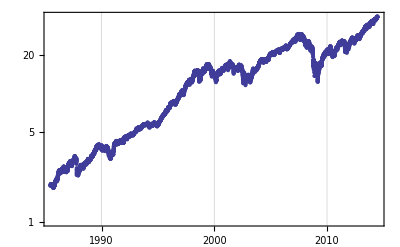

```mathematica
DateListLogPlot[FinancialData["VWNFX",All]]
```

Revisemos alguna fracción de datos de nuestro intéres 01.enero.2011-01-abril.2011

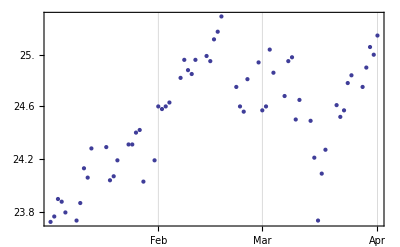

```mathematica
DateListLogPlot[FinancialData["VWNFX",{{2011,1,1},{2011,4,1}}]]
```

Tal vez sea bueno unir los puntos, esto puede ayudar a la parte visual

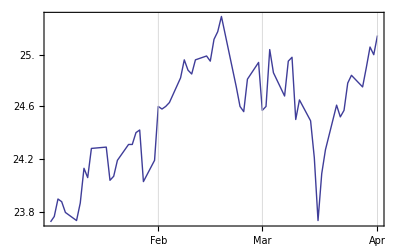

```mathematica
DateListLogPlot[FinancialData["VWNFX",{{2011,1,1},{2011,4,1}}],Joined->True]
```

Lo valioso de esto es que podemos ver y extraer los datos para trabajar, y tambien importarlos

```mathematica
FinancialData["VWNFX",{{2011,1,1},{2011,4,1}}]
```

{{{2011,1,3},23.73},{{2011,1,4},23.77},{{2011,1,5},23.9},{{2011,1,6},23.88},{{2011,1,7},23.8},{{2011,1,10},23.74},{{2011,1,11},23.87},{{2011,1,12},24.13},{{2011,1,13},24.06},{{2011,1,14},24.28},{{2011,1,18},24.29},{{2011,1,19},24.04},{{2011,1,20},24.07},{{2011,1,21},24.19},{{2011,1,24},24.31},{{2011,1,25},24.31},{{2011,1,26},24.4},{{2011,1,27},24.42},{{2011,1,28},24.03},{{2011,1,31},24.19},{{2011,2,1},24.6},{{2011,2,2},24.58},{{2011,2,3},24.6},{{2011,2,4},24.63},{{2011,2,7},24.82},{{2011,2,8},24.96},{{2011,2,9},24.88},{{2011,2,10},24.85},{{2011,2,11},24.96},{{2011,2,14},24.99},{{2011,2,15},24.95},{{2011,2,16},25.12},{{2011,2,17},25.18},{{2011,2,18},25.3},{{2011,2,22},24.75},{{2011,2,23},24.6},{{2011,2,24},24.56},{{2011,2,25},24.81},{{2011,2,28},24.94},{{2011,3,1},24.57},{{2011,3,2},24.6},{{2011,3,3},25.04},{{2011,3,4},24.86},{{2011,3,7},24.68},{{2011,3,8},24.95},{{2011,3,9},24.98},{{2011,3,10},24.5},{{2011,3,11},24.65},{{2011,3,14},24.49},{{2011,3,15},24.21},{{2011,3,16},23.74},{{2011,3,17},24.09},{{2011,3,18},24.27},{{2011,3,21},24.61},{{2011,3,22},24.52},{{2011,3,23},24.57},{{2011,3,24},24.78},{{2011,3,25},24.84},{{2011,3,28},24.75},{{2011,3,29},24.9},{{2011,3,30},25.06},{{2011,3,31},25.},{{2011,4,1},25.15}}

Umm, creo que no es agradable ver los datos de esta manera; pero podemos utilizar unas instrucciones para darle mayor presentación, veamos los datos de 1.Febrero.2011-15.Febrero.2011

```mathematica
Grid[FinancialData["VWNFX",{{2011,2,1},{2011,2,15}}][[1;;11,1;;2]],Frame->All,ItemSize->Automatic,Background->{None,{{LightGray,LightYellow}}}]
```

{2011,2,1} | 24.6
{2011,2,2} | 24.58
{2011,2,3} | 24.6
{2011,2,4} | 24.63
{2011,2,7} | 24.82
{2011,2,8} | 24.96
{2011,2,9} | 24.88
{2011,2,10} | 24.85
{2011,2,11} | 24.96
{2011,2,14} | 24.99
{2011,2,15} | 24.95

```mathematica
FinancialData["VWNFX", {{2011, 1, 1}, {2011, 4, 1}}]
```

{{{2011,1,3},23.73},{{2011,1,4},23.77},{{2011,1,5},23.9},{{2011,1,6},23.88},{{2011,1,7},23.8},{{2011,1,10},23.74},{{2011,1,11},23.87},{{2011,1,12},24.13},{{2011,1,13},24.06},{{2011,1,14},24.28},{{2011,1,18},24.29},{{2011,1,19},24.04},{{2011,1,20},24.07},{{2011,1,21},24.19},{{2011,1,24},24.31},{{2011,1,25},24.31},{{2011,1,26},24.4},{{2011,1,27},24.42},{{2011,1,28},24.03},{{2011,1,31},24.19},{{2011,2,1},24.6},{{2011,2,2},24.58},{{2011,2,3},24.6},{{2011,2,4},24.63},{{2011,2,7},24.82},{{2011,2,8},24.96},{{2011,2,9},24.88},{{2011,2,10},24.85},{{2011,2,11},24.96},{{2011,2,14},24.99},{{2011,2,15},24.95},{{2011,2,16},25.12},{{2011,2,17},25.18},{{2011,2,18},25.3},{{2011,2,22},24.75},{{2011,2,23},24.6},{{2011,2,24},24.56},{{2011,2,25},24.81},{{2011,2,28},24.94},{{2011,3,1},24.57},{{2011,3,2},24.6},{{2011,3,3},25.04},{{2011,3,4},24.86},{{2011,3,7},24.68},{{2011,3,8},24.95},{{2011,3,9},24.98},{{2011,3,10},24.5},{{2011,3,11},24.65},{{2011,3,14},24.49},{{2011,3,15},24.21},{{2011,3,16},23.74},{{2011,3,17},24.09},{{2011,3,18},24.27},{{2011,3,21},24.61},{{2011,3,22},24.52},{{2011,3,23},24.57},{{2011,3,24},24.78},{{2011,3,25},24.84},{{2011,3,28},24.75},{{2011,3,29},24.9},{{2011,3,30},25.06},{{2011,3,31},25.},{{2011,4,1},25.15}}

Por otra parte, algunos de ustedes puede requerir los datos en excel;

```mathematica
Export["misdatos.xlsx",FinancialData["VWNFX",{{2011,1,1},{2011,4,1}}]]
```

misdatos.xlsx

```mathematica
SystemOpen["misdatos.xlsx"]
```

-Graphics-

## Mas ejemplos

Ahora encontremos los  miembros Industrial Dow Jones con baja volatilidad de 50 días:

```mathematica
Select[FinancialData["^DJI","Members"],FinancialData[#,"Volatility50Day"]<0.20&];
FinancialData[#,"StandardName"]&/@%
```

FinancialData::notent: "NotAvailable" is not a known entity, class, or tag for "FinancialData". Use "FinancialData"[] for a list of entities.

Missing[]

Tal vez deseamos saber de alguna otra bolsa, como los primeros miembros de la bolsa de Frankfurt:

```mathematica
Take[FinancialData["Frankfurt","Members"],10]
```

Ok; se que algunos no somos financieros; jeje; entonces probemos lo siguiente

```mathematica
FinancialData[#,"StandardName"]&/@ Take[FinancialData["Frankfurt","Members"],10]
```

de esa forma podemos entender de que compañias hablamos; Ahora veamos el  “Cumulative Returns” para varios fondos de inversión desde 1996 hasta el presente.

```mathematica
fondos = {"VFINX","VEXPX","VWNFX","VWUSX"};
data=
Tooltip[FinancialData[#,"CumulativeReturn",{{1996,1,1},{2011,4,1}}],#]&/@fondos;
DateListPlot[data,Joined->True,Filling->Bottom]
```

Veamos ahora la gráfica de  precios al cierre para el Nikkei 225,  con altos y bajos para cada día durante los últimos 120 días.

```mathematica
DateListPlot[Map[FinancialData["^N225",#1,DatePlus[-120]]&,{"High","Low","Close"}],
Joined->{False,False,True},PlotStyle->Blue,Filling->{1->{2}},FillingStyle->Brown]
```

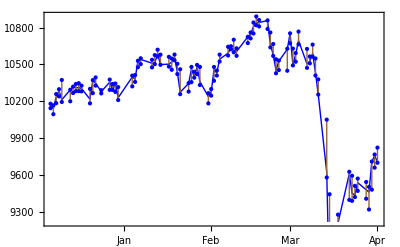

Referencias

Wolfram Research